## From Riccardo:

```mathematica
(* Probs not needed *)
```

```mathematica
argumentLength[func_Symbol] := Lookup[SyntaxInformation[func], "ArgumentsPattern"]
argumentLength["Plot"]
```

## From Giulio and Tim:

### General:

```mathematica
WolframLanguageData["Exp","DocumentationExampleInputs"]
```

```mathematica
SyntaxInformation[Exp]
```

### Defined functions:

```mathematica
(* No longer useful *)
```

```mathematica
parseString[str_String]:=FrontEndExecute[FrontEnd`ReparseBoxStructurePacket[str]];
```

```mathematica
flattenParse[exp_]:=Flatten@ReplaceRepeated[exp, RowBox[{anything___}]:>{anything}]
```

```mathematica
SetAttributes[makeExpressionString, {HoldFirst}]
makeExpressionString[exp_]:=StringTake[ToString[HoldComplete[exp], InputForm], {StringLength["HoldComplete["]+1,-StringLength["]"]-1}]
```

## From Giulio regarding parsing:

```mathematica
ClearAll["Global`*"]
```

#### Convert the expression to a tree structure, regardless of whether it parses or not:

```mathematica
parseInput[str_String]:=ReplaceAll[Replace[FrontEndExecute[FrontEnd`ReparseBoxStructurePacket[str]],RowBox[x_]:>x,{0,Infinity}]," ":> Nothing];
```

```mathematica
(*takepart[expr_String,level_Integer]:=Replace[level[parseInput[expr],{level}],x_/;!AtomQ[x]:>Head[x],{1}]*)
```

#### Get slices of the expression:

```mathematica
getlevel[expr_String,n_Integer]:=With[{el=n},Replace[Level[parseInput[expr],{el}],x_/;!AtomQ[x]:>ToString[Head[x]],{1}]]
```

#### Get all the tree structure of the expression:

```mathematica
getalllevels[expr_String]:=Thread[getlevel[expr,Range[Depth[parseInput[expr]]-1]]];
```

#### functionargs returns the minimum and maximum number of arguments a function can have

```mathematica
(*functionargs[function_]:=Length/@Map[Select[SyntaxInformation[function][[1,2]],#]&,{#==_&,#==_.&,#==OptionsPattern[]&}];*)
```

```mathematica
functionargs[function_String] := functionargs[Symbol[function]]
functionargs[function_Symbol]:=Length/@Map[Select[Lookup[SyntaxInformation[function], "ArgumentsPattern"],#]&,{#==_&,#==_||#==_.||#==OptionsPattern[]&}];
```

#### Playing with uneven number of brackets:

```mathematica
mystring="SortBy[Range[10], Mod[#,3&]";
```

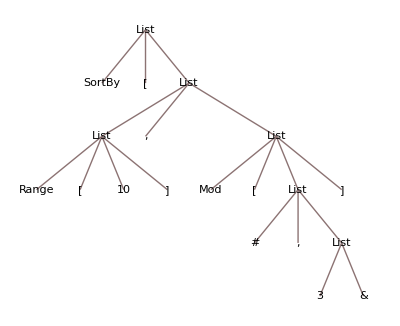

```mathematica
parseInput[mystring]//TreeForm
```

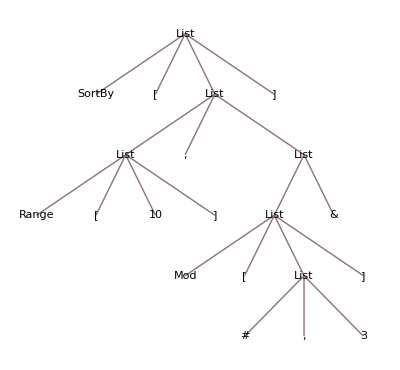

```mathematica
parseInput[mystring]//TreeForm
```

```mathematica
alllevels= getalllevels[mystring];alllevels//Column
```

{SortBy,[,List,]}
{List,,,List}
{Range,[,10,],List,&}
{Mod,[,List,]}
{#,,,3}

```mathematica
listA=Total/@Map[StringCount[#,"["]&,alllevels,{2}]
```

{1,0,1,1,0}

```mathematica
listB=Total/@Map[StringCount[#,"]"]&,alllevels,{2}]
```

{1,0,1,1,0}

```mathematica
Positive[listA-listB]
```

{False,False,False,False,False}

```mathematica
Negative[listA-listB]
```

{False,False,False,False,False}

```mathematica
MapThread[Greater,{listA,listB}]
```

{False,False,False,False,False}

#### Count the # arguments in functions:

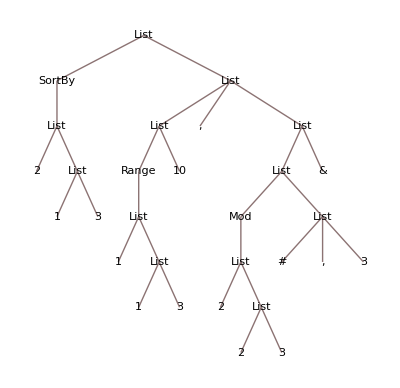

```mathematica
myexpr//. {upper___,function_,open_,body___,close_,lower___}/; open=="["&&close=="]"  :> { function[{1+Length@Cases[","]@body,functionargs[function]}], body, lower}//TreeForm
```

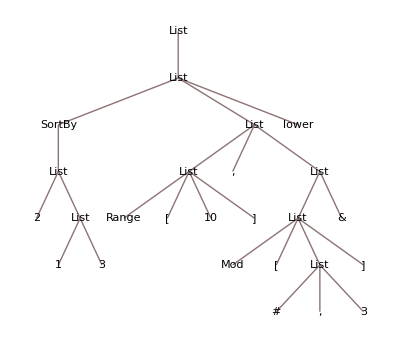

```mathematica
SequenceCases[myexpr,{function_,open_,body___,close_}/; open=="["&&close=="]":> { function[{1+Length@Cases[","]@body,functionargs[function]}], body, lower}] //TreeForm
```

#### Other stuff:

-Graphics-

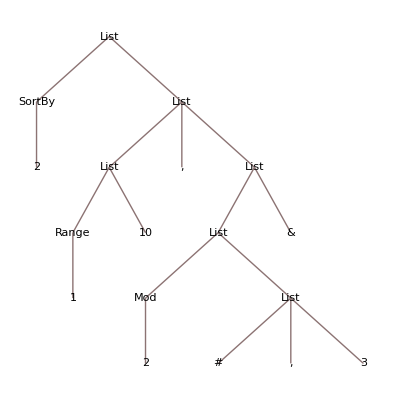

```mathematica
myexpr=parseInput[mystring];myexpr//TreeForm
```

```mathematica
myexpr/. {"["__}->  "[["//TreeForm
```

-Graphics-

```mathematica
data={7,2,4,9,8,6,1,4,2};
```

```mathematica
data//.{upper___,a_,c_,b_,lower___}/;a>b->{upper,b,c,a,lower}
```

{1,2,2,4,4,6,7,9,8}

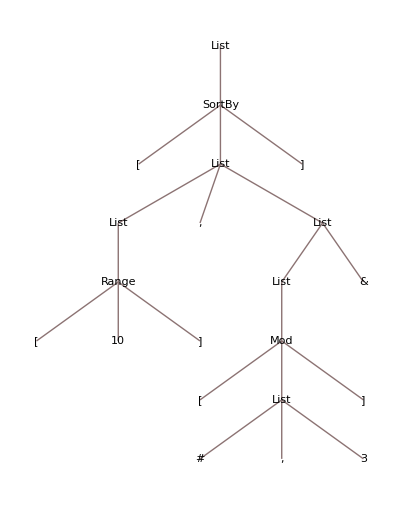

```mathematica
mynewexpression//TreeForm
```

```mathematica
myexpr//. {upper___,function_,open_,body___,close_,lower___}/; open=="["&&close=="]" /; Echo[{function, !AtomQ[body]/.bodypart_/;!AtomQ[bodypart]:>ToString[Head[bodypart]] },"Body:"]:> {upper, function, body, lower}//TreeForm
```

Body: {SortBy,True}

Body: {Range,False}

Body: {Mod,True}

```mathematica
myexpr//. {upper___,function_,open_,body___,close_,lower___}/; open=="["&&close=="]"  :> {upper, function[1+Length@Cases[","]@body], body, lower}//TreeForm
```

-Graphics-

```mathematica
myexpr//TreeForm
```

-Graphics-

```mathematica
Cases[myexpr,{upper___,function_,open_,body___,close_,lower___}]
```

{{{Range,[,10,]},,,{{Mod,[,{#,,,3},]},&}}}

```mathematica
mynewexpression=myexpr//. {upper___,function_,open_,body___,close_,lower___}/; open=="["&&close=="]" :> {upper, function["[", body,"]"], lower}//TreeForm
```

-Graphics-

```mathematica
(*/;Echo[{body,Length[body]},"Body Length"] *)
```

```mathematica
myexpr//TreeForm
```

-Graphics-

```mathematica
Cases[myexpr,{___,open_,body___,close_,___},Depth[myexpr]]//Column
```

{Range,[,10,]}
{#,,,3}
{Mod,[,{#,,,3},]}
{{Mod,[,{#,,,3},]},&}
{{Range,[,10,]},,,{{Mod,[,{#,,,3},]},&}}

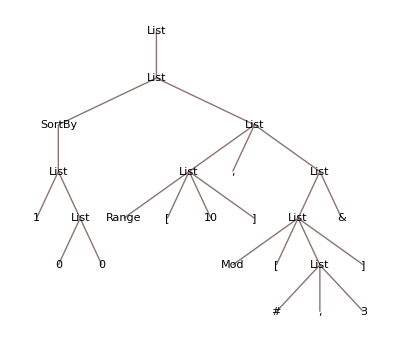

```mathematica
/; open=="["&&close=="]"
```